#### Function list dump

pipe
pipeList
branch
branchSeq
deCurry
nativeSize
checkerboard
gammaDecode
gammaEncode
imgGammaDecode
imgGammaEncode
levelIndentFunc
horizontalTreeForm
GraphEdgeSleek
toRegularArray
inputHistoryViewer
StringSplitNested
colorFromHex
colorToHex
DatasetGrid
multiDimGrid

```mathematica
Needs["SilviaCollection`"]
```

```mathematica
x//pipe[f,h,g]
```

g[h[f[x]]]

```mathematica
x//pipeList[f,h,g]
```

{x,f[x],h[f[x]],g[h[f[x]]]}

```mathematica
x//branch[f,h,g]
```

{f[x],h[x],g[x]}

```mathematica
x//branchSeq[f,h,g]//F
```

F[f[x],h[x],g[x]]

```mathematica
f[1,2,3,4]//deCurry
```

f[1][2][3][4]

Gamma correction is important:

```mathematica
{
ConstantImage[RGBColor[0.1725, 0.5767499999999999, 0.75],{101,101}]
,ConstantImage[RGBColor[0.88, 0.2024, 0.2024],{101,101}]
,Image[GaussianMatrix[{50,30}]//Rescale]
}//pipeList[
branch[First,pipe[Rest,Apply@SetAlphaChannel]]
,branch[Identity,Map@pipe[branchSeq[pipe[RemoveAlphaChannel,imgGammaDecode],AlphaChannel],SetAlphaChannel]]
,ImageCompose@@@#&,Map@RemoveAlphaChannel
,branch[First,pipe[Last,imgGammaEncode]]
]//pipe[
Rest,Append[{"↑ wrong blend","↑ correct blend"}]
,Grid[#,Frame->All,ItemSize->Full]&
]
```

-Graphics- | -Graphics-
{-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
↑ wrong blend | ↑ correct blend

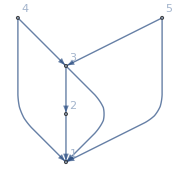

```mathematica
mygraph=Graph[{1,2,3,4,5},{2->1,3->1,3->2,4->1,4->3,5->1,5->3},VertexLabels->"Name",ImageSize->Small]
```

```mathematica
mygraph//GraphEdgeSleek
```

-Graphics-

```mathematica
RandomInteger[{0,9},{2,3,4,2,1,2,3}]//multiDimGrid
```

| 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 |  | 1 |  |  |  |  | 2 |  |  |  |  | 3 |  |  |  |  | 4 |  |  |  |  |  | 1 |  |  |  |  | 2 |  |  |  |  | 3 |  |  |  |  | 4 |  |  |  | 
 | 1 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 1 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  |  | 1 | 6 | 4 | 7 |  | 1 | 9 | 4 | 5 |  | 1 | 3 | 2 | 2 |  | 1 | 3 | 8 | 0 |  |  | 1 | 7 | 4 | 8 |  | 1 | 2 | 4 | 5 |  | 1 | 7 | 2 | 9 |  | 1 | 9 | 4 | 6
 |  |  | 2 | 3 | 2 | 3 |  | 2 | 2 | 1 | 2 |  | 2 | 7 | 1 | 2 |  | 2 | 8 | 7 | 6 |  |  | 2 | 6 | 4 | 4 |  | 2 | 9 | 8 | 6 |  | 2 | 3 | 6 | 0 |  | 2 | 6 | 8 | 4
 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  |  | 1 | 2 | 0 | 1 |  | 1 | 2 | 4 | 5 |  | 1 | 3 | 3 | 3 |  | 1 | 6 | 3 | 5 |  |  | 1 | 0 | 3 | 1 |  | 1 | 8 | 7 | 3 |  | 1 | 4 | 1 | 9 |  | 1 | 4 | 3 | 2
 |  |  | 2 | 0 | 4 | 4 |  | 2 | 8 | 6 | 9 |  | 2 | 9 | 3 | 5 |  | 2 | 8 | 0 | 2 |  |  | 2 | 6 | 7 | 9 |  | 2 | 6 | 5 | 9 |  | 2 | 3 | 8 | 9 |  | 2 | 3 | 9 | 4
 | 2 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 2 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  |  | 1 | 2 | 8 | 0 |  | 1 | 9 | 4 | 5 |  | 1 | 7 | 3 | 4 |  | 1 | 2 | 8 | 7 |  |  | 1 | 6 | 9 | 9 |  | 1 | 7 | 0 | 5 |  | 1 | 4 | 4 | 8 |  | 1 | 4 | 0 | 8
 |  |  | 2 | 8 | 7 | 8 |  | 2 | 4 | 2 | 7 |  | 2 | 4 | 9 | 6 |  | 2 | 8 | 7 | 5 |  |  | 2 | 2 | 9 | 5 |  | 2 | 7 | 1 | 0 |  | 2 | 5 | 3 | 7 |  | 2 | 0 | 2 | 6
 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  |  | 1 | 4 | 1 | 9 |  | 1 | 9 | 9 | 7 |  | 1 | 0 | 3 | 7 |  | 1 | 9 | 5 | 1 |  |  | 1 | 5 | 2 | 2 |  | 1 | 6 | 9 | 5 |  | 1 | 3 | 2 | 0 |  | 1 | 8 | 0 | 3
 |  |  | 2 | 5 | 6 | 1 |  | 2 | 9 | 4 | 8 |  | 2 | 3 | 8 | 6 |  | 2 | 0 | 1 | 6 |  |  | 2 | 9 | 8 | 6 |  | 2 | 4 | 7 | 8 |  | 2 | 0 | 9 | 3 |  | 2 | 1 | 9 | 9
 | 3 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  | 3 |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  |  |  | 1 |  |  | 
 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 |  | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3 | 1 |  | 1 | 2 | 3
 |  |  | 1 | 1 | 9 | 8 |  | 1 | 1 | 1 | 7 |  | 1 | 1 | 7 | 0 |  | 1 | 3 | 6 | 0 |  |  | 1 | 9 | 4 | 9 |  | 1 | 1 | 2 | 7 |  | 1 | 5 | 8 | 3 |  | 1 | 8 | 3 | 8
 |  |  | 2 | 2 | 4 | 7 |  | 2 | 6 | 2 | 3 |  | 2 | 8 | 8 | 5 |  | 2 | 4 | 0 | 8 |  |  | 2 | 2 | 0 | 7 |  | 2 | 6 | 1 | 7 |  | 2 | 5 | 8 | 6 |  | 2 | 1 | 2 | 2
 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 |  | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3 | 2 |  | 1 | 2 | 3
 |  |  | 1 | 9 | 6 | 0 |  | 1 | 3 | 2 | 4 |  | 1 | 0 | 7 | 2 |  | 1 | 2 | 6 | 1 |  |  | 1 | 7 | 0 | 3 |  | 1 | 5 | 0 | 9 |  | 1 | 6 | 9 | 1 |  | 1 | 1 | 8 | 2
 |  |  | 2 | 7 | 7 | 6 |  | 2 | 8 | 3 | 0 |  | 2 | 9 | 2 | 6 |  | 2 | 5 | 8 | 1 |  |  | 2 | 5 | 1 | 3 |  | 2 | 6 | 5 | 8 |  | 2 | 4 | 5 | 4 |  | 2 | 6 | 3 | 3